```mathematica
E0[h_,m_,k_]:=(h^2 k^2)/(2m)
```

```mathematica
thing[h_,m_,k_,K_,U_]:= (E0[h,m,k]+E0[h,m,k-K])/2+Sqrt[((E0[h,m,k]-E0[h,m,k-K])/2)^2+U^2]
```

```mathematica
thing2[h_,m_,k_,K_,U_]:= (E0[h,m,k]+E0[h,m,k-K])/2-Sqrt[((E0[h,m,k]-E0[h,m,k-K])/2)^2+U^2]
```

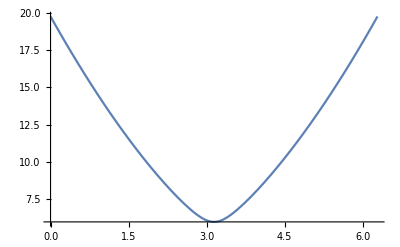

```mathematica
Plot[thing[1,1,k,2Pi,1],{k,0,2Pi}]
```

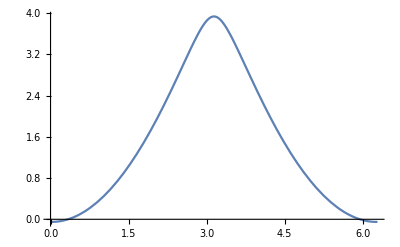

```mathematica
Plot[thing2[1,1,k,2Pi,1],{k,0,2Pi}]
```

```mathematica
max=100*FindMinimum[thing[1,1,k,1,0.01],{k,0.5}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{13.5,{100 (k→0.5)}}

```mathematica
min=100*FindMaximum[thing2[1,1,k,1,0.01],{k,0.5}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{11.5,{100 (k→0.5)}}

```mathematica
Plot[{thing[10,1,k,1,1],thing2[10,1,k,1,1]},{k,0,0.5},PlotRange->{0,30},BoxRatios{1,2}]
```

Plot::nonopt: Options expected (instead of BoxRatios {1,2}) beyond position 2 in Plot[{thing[10,1,k,1,1],thing2[10,1,k,1,1]},{k,0,0.5},PlotRange→{0,30},BoxRatios {1,2}]. An option must be a rule or a list of rules.

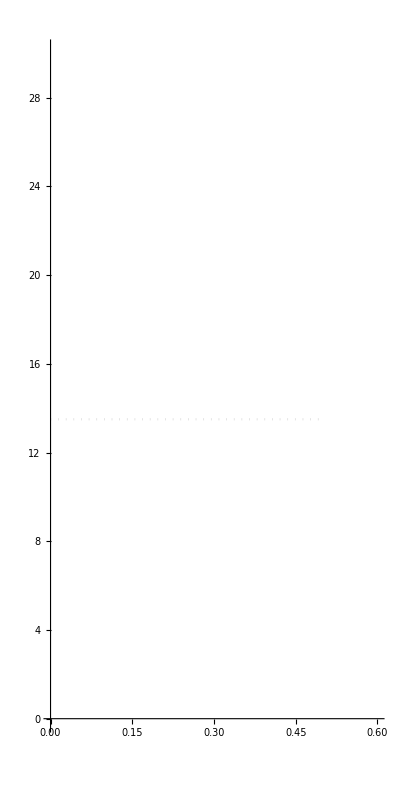

```mathematica
lines=Plot[max,{k,0,0.5},PlotRange->{{0,0.6},{0,30}},AspectRatio->2,PlotStyle->{{Dotted,LightGray}}]
```

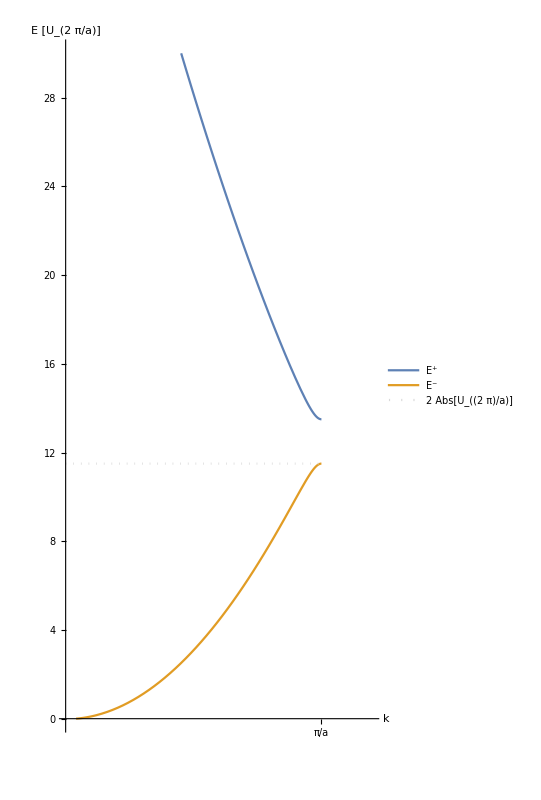

```mathematica
curves=Plot[{100*thing[1,1,k,1,0.01],100*thing2[1,1,k,1,0.01],min},{k,0,0.5},PlotRange->{{0,0.6},{0,30}},PlotStyle->{Automatic,Automatic,{Dotted,LightGray}},AspectRatio->2,AxesLabel->{"k","E   [U_(2  π/a)]"},PlotLegends->{"E^+","E^-",2Abs[Subscript[U, 2π/a]]},Ticks->{{{0.5,π/a}},Automatic}]
```

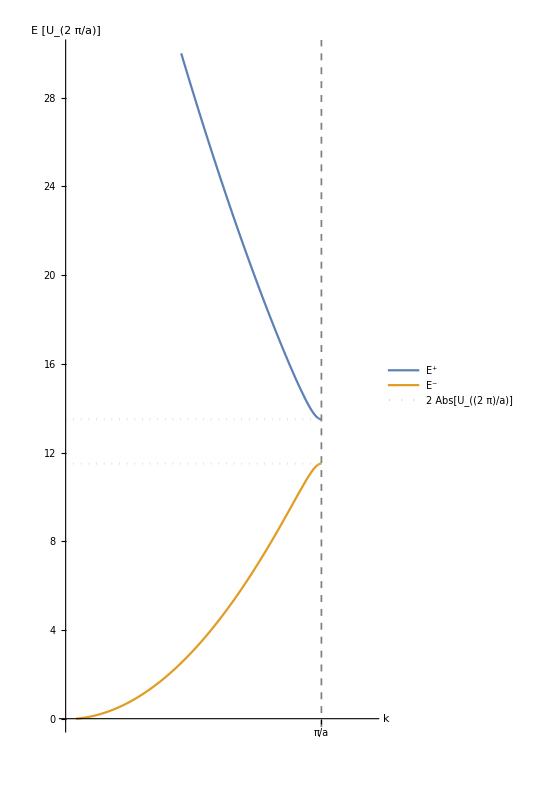

```mathematica
Show[curves,lines,Epilog->{Gray,Dashed,AbsoluteThickness[1.25],Line[{{0.5,-1},{0.5,31}}]}]
```

```mathematica
D[(1-k^2/kF^2)/(4k/kF)Log[Abs[(1+k/kF)/(1-k/kF)]],k]
```

-Log[Abs[(1+k/kF)/(1-k/kF)]]/(2 kF)-((1-k^2/kF^2) kF Log[Abs[(1+k/kF)/(1-k/kF)]])/(4 k^2)+((1-k^2/kF^2) (1/((1-k/kF) kF)+(1+k/kF)/((1-k/kF)^2 kF)) kF Abs'[(1+k/kF)/(1-k/kF)])/(4 k Abs[(1+k/kF)/(1-k/kF)])

```mathematica
Series[(1-x^2)/(4x)Log[Abs[(1+x)/(1-x)]],{x,0,0}]
```

Log[Abs[(1+x)/(1-x)]] (1/(4 x)+O[x]^1)

```mathematica
D[1/(4k/kF)Log[Abs[(1+k/kF)/(1-k/kF)]],k]
```

-(kF Log[Abs[(1+k/kF)/(1-k/kF)]])/(4 k^2)+((1/((1-k/kF) kF)+(1+k/kF)/((1-k/kF)^2 kF)) kF Abs'[(1+k/kF)/(1-k/kF)])/(4 k Abs[(1+k/kF)/(1-k/kF)])